Program calculating bound states for dipole-dipole interaction for a given short-range phase
Everything in units of R_d and E_d (characteristic length and energy for dipole-dipole interaction)

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Oem\Desktop\Dipoles final

Parameters:
β = (R_v/R_d)^4
Lmax - maximal value of angular momentum L
xi - minimal value of r in the grid
xf -maximal value of r in the grid
nptl - number of points to tabulate the wavelenght
npt - numeber of point per de Broglie wavelenght in the grid 
emin - mimimal energy for bound state searching
emax - maximal energy for bound state searching
epsf - small number used to determine final point of integration
nptf - number of points to tabulate the final point of integration

```mathematica
Lmax=86;xi=0.28;xf=400;Id=IdentityMatrix[Lmax/2+1];nptl=200;npt=20;epsf=10^-3;epsi=10^-3;nptf=50;dxf=10;
freq=30000; 
freqz=0.1 freq;
d=10/(137*2);
m = 9.18 BohrM;
BohrM = 1.3996 (*MHz/Gauss*)
dp=0.2;
phimin =- N[π/2-0.01];
phimax=N[π/2-0.01];
```

1.3996

Conversion factor from Hz to Eh

```mathematica
HztoEh=1.519829 10^(-16);
```

Debye  in atomic units

```mathematica
Debye=0.393456;
```

Mass unit  in atomic units

```mathematica
massunit=1.661 10^(-24)/(9.110 10^(-28)); (*Unit/Masa elektronu*)
```

Parameters for Dy atoms

```mathematica
μ=81.25 massunit; (*Masa zredukowana*)
```

```mathematica
C6=2277;
```

```mathematica
Dperm=0.22 Debye;
```

Trap frequency and harm. osc. length

```mathematica
ω=2 π freq HztoEh; ωz=2 π freqz HztoEh;aHO=(1/Sqrt[μ ω])/R6; aHOz=(1/Sqrt[μ ωz])/R6
(*ωz=2 π freqz HztoEh;aHOz=(1/Sqrt[μ ωz])/R6*)
```

9.52462

van der Waals length and energy

```mathematica
R6=(2 μ C6)^(1/4)
E6=1/(2 μ R6^2)
```

161.164

1.29946×10^-10

Characteristic length and energy for dipole-dipole interaction (vdw units)

```mathematica
C3=2d^2;R3=2 μ C3/R6;E3=(1/(2μ (R6 R3)^2))/E6;
β=R3
R3
```

4.89741

4.89741

Harmonic oscillator energy in vdW units

```mathematica
α=(1/aHO)^4
αz=(1/aHOz)^4;
```

0.0121509

```mathematica
Ω=2 Sqrt[α];
Ωz=2 Sqrt[αz]
```

0.0220462

```mathematica
α=(Ω/2)^2;
αz=(Ωz/2)^2
```

0.000121509

Energy scale

```mathematica
emin=-0.001 Ωz ;emax=-20 Ωz;
```

Mean scattering length of vdW potential

```mathematica
abar=2 Pi/Gamma[1/4]^2;abar1=Gamma[1/4]^6/(144 Pi^2 Gamma[3/4]^2)abar ;aHO/abar
```

6.3013

Spherical Bessel functions

```mathematica
jl[l_,x_]:=Sqrt[Pi/(2x)]BesselJ[l+1/2,x];nl[l_,x_]:=(-1)^(l+1) Sqrt[Pi/(2x)]BesselJ[-l-1/2,x]
```

Potentials

```mathematica
Vho[l1_,ml1_,l2_,ml2_]:= (If[l1==l2,1,0]If[ml1==ml2,1,0]-(1-αz/α)If[ml1==ml2,1,0]/3((-1)^ml1 Sqrt[2 l1 +1]Sqrt[2l2 +1] 2 ThreeJSymbol[{l1,0},{2,0},{l2,0}]ThreeJSymbol[{l1,-ml1},{2,0},{l2,ml2}] + If[l1==l2,1,0]));
Vedd[l1_,ml1_,l2_,ml2_]:=-(-1)^ml1 Sqrt[2 l1 +1]Sqrt[2l2 +1]  ThreeJSymbol[{l1,0},{2,0},{l2,0}]ThreeJSymbol[{l1,-ml1},{2,0},{l2,ml2}];(*Dodać symbol wignera*)
Vmdd[l1_,ml1_,l2_,ml2_]:=-(-1)^ml1 Sqrt[2 l1 +1]Sqrt[2l2 +1]  ThreeJSymbol[{l1,0},{2,0},{l2,0}]ThreeJSymbol[{l1,-ml1},{2,0},{l2,ml2}];
Vvdw[l1_,ml1_,l2_,ml2_]:= -If[l1==l2,1,0]If[ml1==ml2,1,0];
```

```mathematica
Veddtab=Developer`ToPackedArray[N[Table[Vedd[l1,0,l2,0],{l1,0,Lmax,2},{l2,0,Lmax,2}]]];
Vmddtab=Developer`ToPackedArray[N[Table[Vmdd[l1,0,l2,0],{l1,0,Lmax,2},{l2,0,Lmax,2}]]];
Vvdwtab=Developer`ToPackedArray[N[Table[Vvdw[l1,0,l2,0],{l1,0,Lmax,2},{l2,0,Lmax,2}]]];
Vhotab=Developer`ToPackedArray[N[Table[Vho[l1,0,l2,0],{l1,0,Lmax,2},{l2,0,Lmax,2}]]];
Vcftab = Developer`ToPackedArray[N[Table[If[l1==l2,l1(l1+1),0],{l1,0,Lmax,2},{l2,0,Lmax,2}]]];
Veddtab2=Developer`ToPackedArray[N[Table[Vedd[l1,0,l2,0],{l1,1,Lmax,2},{l2,1,Lmax,2}]]];
Vmddtab2=Developer`ToPackedArray[N[Table[Vmdd[l1,0,l2,0],{l1,1,Lmax,2},{l2,1,Lmax,2}]]];
Vvdwtab2=Developer`ToPackedArray[N[Table[Vvdw[l1,0,l2,0],{l1,1,Lmax,2},{l2,1,Lmax,2}]]];
Vhotab2=Developer`ToPackedArray[N[Table[Vho[l1,0,l2,0],{l1,1,Lmax,2},{l2,1,Lmax,2}]]];
Vcftab2 = Developer`ToPackedArray[N[Table[If[l1==l2,l1(l1+1),0],{l1,1,Lmax,2},{l2,1,Lmax,2}]]];
```

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{0,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{4,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{0,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{4,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{0,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{4,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{5,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{7,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{5,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{7,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{5,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{7,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

```mathematica
Vhotable[x_]:=N[(Table[Vhotab[[l1/2+1,l2/2+1]],{l1,0,Lmax,2},{l2,0,Lmax,2}])/.{r->x}];
Veddtable[x_]:=N[(Table[Veddtab[[l1/2+1,l2/2+1]],{l1,0,Lmax,2},{l2,0,Lmax,2}])/.{r->x}];
```

```mathematica
1/α Vhotable[1]//MatrixForm
1/β Veddtable[1]//MatrixForm
```

(55.1399 | -24.2913 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-24.2913 | 39.6208 | -20.8211 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -20.8211 | 41.0316 | -20.5429 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -20.5429 | 41.3138 | -20.461 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -20.461 | 41.4178 | -20.4259 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -20.4259 | 41.4675 | -20.4077 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -20.4077 | 41.4951 | -20.3969 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | -20.3969 | 41.512 | -20.3901 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3901 | 41.5231 | -20.3855 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3855 | 41.5308 | -20.3823 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3823 | 41.5364 | -20.3799 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3799 | 41.5405 | -20.3781 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3781 | 41.5437 | -20.3767 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3767 | 41.5462 | -20.3756 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3756 | 41.5481 | -20.3747 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3747 | 41.5497 | -20.374 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.374 | 41.551 | -20.3734 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3734 | 41.5521 | -20.3729 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3729 | 41.553 | -20.3725 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3725 | 41.5538 | -20.3721 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3721 | 41.5545 | -20.3718 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3718 | 41.5551 | -20.3715 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3715 | 41.5555 | -20.3713 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3713 | 41.556 | -20.3711 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3711 | 41.5564 | -20.3709 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3709 | 41.5567 | -20.3708 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3708 | 41.557 | -20.3706 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3706 | 41.5573 | -20.3705 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3705 | 41.5575 | -20.3704 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3704 | 41.5577 | -20.3703 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3703 | 41.5579 | -20.3702 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3702 | 41.5581 | -20.3701 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3701 | 41.5582 | -20.37 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.37 | 41.5584 | -20.37 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.37 | 41.5585 | -20.3699 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3699 | 41.5586 | -20.3699 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3699 | 41.5588 | -20.3698 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3698 | 41.5589 | -20.3697 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3697 | 41.559 | -20.3697 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3697 | 41.559 | -20.3697 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3697 | 41.5591 | -20.3696 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3696 | 41.5592 | -20.3696 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3696 | 41.5593 | -20.3696
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -20.3696 | 41.5593)

(0. | -0.0913163 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.0913163 | -0.0583399 | -0.0782711 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.0782711 | -0.0530362 | -0.0772254 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -0.0772254 | -0.0519755 | -0.0769175 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -0.0769175 | -0.0515847 | -0.0767855 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -0.0767855 | -0.0513978 | -0.0767169 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -0.0767169 | -0.051294 | -0.0766767 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | -0.0766767 | -0.0512303 | -0.0766511 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0766511 | -0.0511885 | -0.0766338 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0766338 | -0.0511596 | -0.0766215 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0766215 | -0.0511387 | -0.0766126 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0766126 | -0.0511232 | -0.0766058 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0766058 | -0.0511113 | -0.0766005 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0766005 | -0.051102 | -0.0765964 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765964 | -0.0510946 | -0.0765931 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765931 | -0.0510886 | -0.0765904 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765904 | -0.0510837 | -0.0765881 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765881 | -0.0510796 | -0.0765863 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765863 | -0.0510761 | -0.0765847 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765847 | -0.0510732 | -0.0765833 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765833 | -0.0510707 | -0.0765822 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765822 | -0.0510686 | -0.0765812 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765812 | -0.0510667 | -0.0765803 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765803 | -0.0510651 | -0.0765796 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765796 | -0.0510637 | -0.0765789 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765789 | -0.0510624 | -0.0765783 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765783 | -0.0510613 | -0.0765778 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765778 | -0.0510603 | -0.0765773 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765773 | -0.0510594 | -0.0765769 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765769 | -0.0510586 | -0.0765765 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765765 | -0.0510578 | -0.0765761 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765761 | -0.0510572 | -0.0765758 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765758 | -0.0510566 | -0.0765755 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765755 | -0.051056 | -0.0765753 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765753 | -0.0510555 | -0.076575 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.076575 | -0.0510551 | -0.0765748 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765748 | -0.0510547 | -0.0765746 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765746 | -0.0510543 | -0.0765744 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765744 | -0.0510539 | -0.0765743 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765743 | -0.0510536 | -0.0765741 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765741 | -0.0510533 | -0.0765739 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765739 | -0.051053 | -0.0765738 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765738 | -0.0510527 | -0.0765737
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0765737 | -0.0510525)

Matrix containg potential

```mathematica
V[r_]:=1/r^2 Vcftab + 1/r^6 Vvdwtab +β/r^3 Veddtab+α r^2 Vhotab;
V2[r_]:=1/r^2 Vcftab2 + 1/r^6 Vvdwtab2 +β/r^3 Veddtab2+α r^2 Vhotab2;
```

```mathematica
V[1]//MatrixForm
Id//MatrixForm
ref =Table[10,{n,1,Lmax/2+1}]
refdiag = DiagonalMatrix[ref]//MatrixForm
```

(-0.991859 | -2.19378 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-2.19378 | 3.60659 | -1.88038 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -1.88038 | 17.734 | -1.85526 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -1.85526 | 39.7595 | -1.84786 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -1.84786 | 69.7689 | -1.84469 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -1.84469 | 107.773 | -1.84304 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -1.84304 | 153.776 | -1.84207 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | -1.84207 | 207.777 | -1.84146 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.84146 | 269.778 | -1.84104 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.84104 | 339.779 | -1.84075 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.84075 | 417.78 | -1.84053 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.84053 | 503.78 | -1.84037 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.84037 | 597.78 | -1.84024 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.84024 | 699.78 | -1.84015 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.84015 | 809.781 | -1.84007 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.84007 | 927.781 | -1.84 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.84 | 1053.78 | -1.83995 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.83995 | 1187.78 | -1.8399 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.8399 | 1329.78 | -1.83986 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.83986 | 1479.78 | -1.83983 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.83983 | 1637.78 | -1.8398 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.8398 | 1803.78 | -1.83978 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.83978 | 1977.78 | -1.83976 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.83976 | 2159.78 | -1.83974 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.83974 | 2349.78 | -1.83972 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.83972 | 2547.78 | -1.83971 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.83971 | 2753.78 | -1.8397 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.8397 | 2967.78 | -1.83969 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.83969 | 3189.78 | -1.83968 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.83968 | 3419.78 | -1.83967 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.83967 | 3657.78 | -1.83966 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.83966 | 3903.78 | -1.83965 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.83965 | 4157.78 | -1.83964 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.83964 | 4419.78 | -1.83964 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.83964 | 4689.78 | -1.83963 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.83963 | 4967.78 | -1.83963 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.83963 | 5253.78 | -1.83962 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.83962 | 5547.78 | -1.83962 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.83962 | 5849.78 | -1.83961 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.83961 | 6159.78 | -1.83961 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.83961 | 6477.78 | -1.83961 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.83961 | 6803.78 | -1.8396 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.8396 | 7137.78 | -1.8396
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.8396 | 7479.78)

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

{10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10}

(10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10)

Short range solution for van der Waals potential, with the short range phase "phi"

```mathematica
sol0[l_,r_,phi_]=Sin[phi] Sqrt[r]BesselJ[1/4,1/(2 r^2)]+Cos[phi]Sqrt[r] BesselY[1/4,1/(2 r^2)];(*nie ma l*)
```

Table of short range solutions

```mathematica
Psi0[r_,ph_]:=Table[If[l1==l2,sol0[l1,r,ph],0] ,{l1,0,Lmax,2},{l2,0,Lmax,2}]
```

Adiabatic potentials (diagonalized V[r]) + van der Waals potential

```mathematica
(*LogLinearPlot[{1/Ωz(Take[Sort[Eigenvalues[V[x]]],Lmax/2+1]),1/Ωz(Take[Sort[Eigenvalues[V2[x]]],Lmax/2])},{x,0.5,xf},
PlotRange->{-0.5,200},AxesOrigin->{0.5,0},
AspectRatio->0.75,
Frame->True, FrameStyle->{{Directive[Thickness[0.005],Black],Directive[Thickness[0.005],Black]},{Directive[Thickness[0.005],Black],Directive[Thickness[0.005],Black]}},
PlotStyle->{Thick,{Red,Dashed}},PlotLegends->Placed[LineLegend[{Style["Bosonic",FontFamily->"Times",FontWeight->Bold],Style["Fermionic",FontFamily->"Times",FontWeight->Bold]}, LegendLabel->Style["Collision channels",FontSize->14, FontFamily->"Times",FontWeight->Bold],LegendFunction->(Framed[#,RoundingRadius->0,Background->White]&),LegendMargins->5],{Left,Top}],FrameLabel->{Style["r (R_vdW)",FontSize->20, FontFamily->"Times New Roman",FontWeight->Bold],Style["Adiabatic energies (E_ω)",FontSize->20,FontWeight->Bold, FontFamily->"Times"]},GridLines->Automatic, GridLinesStyle->Directive[Thin, Dashed, LightGray],ImagePadding->50,ImageSize->500]*)
```

Subroutine determining final point of integration versus energy. This speeds up the numerical calculations. The plot shows final point of integration versus Log[10,-E]

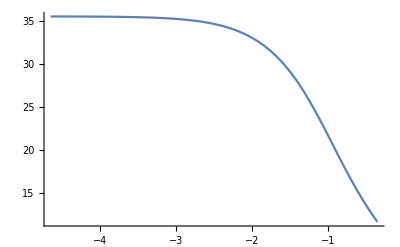

```mathematica
Module[{pemin,pemax,dp,TurnPoint,k,ExpInt,p,x,tabf},TurnPoint[e_?NumericQ]:=x/.FindRoot[e+1/x^6-αz x^2==0,{x,xi,xf}][[1]];(*Przybliżenie WKB*)
k[x_,e_]:=Sqrt[-(e+1/x^6-αz x^2)];
ExpInt[rf_?NumericQ,e_?NumericQ]:=NIntegrate[k[x,e],{x,TurnPoint[e],rf}];
pemin=Log[10,-emin];
pemax=Log[10,-emax];
tabf=Table[{p,x/.FindRoot[Exp[-ExpInt[x,-10^p]]==epsf,{x,TurnPoint[-10^p],xf}][[1]]},{p,pemin,pemax,(pemax-pemin)/nptf}];xfin=Interpolation[tabf];
Plot[xfin[x],{x,pemin,pemax}]]
```

Subroutine determining steps
Parameters:
npt -  number of points per one wave-lenght

InterpolatingFunction::dmval: Input value {0.100039} lies outside the range of data in the interpolating function. Extrapolation will be used.

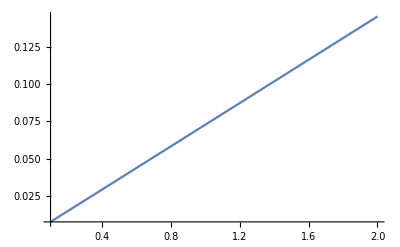

```mathematica
Module[{tab,eig,lambda,h,dbl,n},

tab=Table[eig=Eigenvalues[V[x]];{x,Min[Flatten[{2Pi/Sqrt[Abs[emin-eig]],2Pi/Sqrt[Abs[emax-eig]]}]]},{x,xi,xf,(xf-xi)/nptl}];
lambda=Interpolation[tab]; (*Local de Broglie wavelength (minimum over all channels). Used for determination of the step size *)

xt={};
h=lambda[xi]/npt;
AppendTo[xt,xi];
AppendTo[xt,xi+h];
dbl=1; (* dbl = 1 - step doubling or halving was done in the previous step, dbl = 0 otherwise *)
n=2;

While[(xt[[n]]<xf)||(dbl==1),
Which[
(lambda[xt[[n]]]≥2 npt h)&&(dbl==0),

h=2h;
AppendTo[xt,xt[[n]]+h];
dbl=1;,

(lambda[xt[[n]]]<npt h)&&(dbl==0),

h=h/2;
AppendTo[xt,xt[[n]]+h];
dbl=1;,

True,

AppendTo[xt,xt[[n]]+h];
dbl=0;
];
n++;
];
nstep=n;  (* Total number of steps *);
Plot[lambda[x],{x,0.1,2},PlotRange->All]
]
```

Number of steps

```mathematica
nstep
```

42806

Matching point (somewhere between xi and xf in the classically allowed regime). It position is determined versus position of the classical turning point for highest L

```mathematica
xmid=1
```

1

Location of the matching point in the table xt

```mathematica
nmid=1; 
While[xt[[nmid]]<xmid,nmid++];
nmid--
xt[[nmid]]
```

490

0.998911

Subroutine performing outward integration using renormalized Numerov method
It takes Psi0 as an initial condition

Parameters:
en - energy
n0 -  starting point (element of xt)
nf -  final point (element of xt)
phi - short-range phase
cl: if 1 clears table Rout (to save memory)

```mathematica
evolNumOut[en_?NumericQ,n0_?IntegerQ,nf_?IntegerQ,phi_?NumericQ,cl_?IntegerQ]:=
Module[{W,Qt,n,Rinv,h,h0,nodes,Ro},

nodes=0;

Rout[n0]=Psi0[xt[[n0+1]],phi].Inverse[Psi0[xt[[n0]],phi]];
nodes+=Length[Select[Eigenvalues[Rout[n0]],#<0&]];(*Which functions change sign*)
h=xt[[n0+1]]-xt[[n0]];
n=n0+1;

While[n<=nf,
h0=h;
h=xt[[n+1]]-xt[[n]];
Which[

Abs[h]>1.5 Abs[h0],
W=Id+(h^2/12) QT[[n+1]];
Rout[n]=Inverse[W].(2 Id -(5h^2/6)QT[[n]]-(Id+(h^2/12)QT[[n-2]]).Inverse[Rout[n-1].Rout[n-2]]);,

Abs[h]<0.75 Abs[h0],
Qt=(en + ref[[1]])Id-V[(xt[[n]]+xt[[n-1]])/2];
Rinv=Inverse[2 Id-(h0^2/12)Qt].((Id+(h0^2/12)QT[[n-1]]).Inverse[Rout[n-1]]+Id+(h0^2/12)QT[[n]]);
W=Id+(h^2/12) QT[[n+1]];
Rout[n]=Inverse[W].((2 Id -(5h^2/6)QT[[n]])-(Id+(h^2/12)Qt).Rinv);,

True,
W=Id+(h^2/12) QT[[n+1]];
Rout[n]=Inverse[W].((2 Id -(5h^2/6)QT[[n]])-(Id+(h^2/12)QT[[n-1]]).Inverse[Rout[n-1]]);
];
nodes+=Length[Select[Eigenvalues[Rout[n]],#<0&]];
n++;
];
Ro=Rout[nf];
Clear[W,Qt,n,Rinv,h,h0];
If[cl==1,Clear[Rout]];
{Ro,nodes}]
```

Subroutine performing inward integration using renormalized Noumerov method
It assumes that function vanishes at the starting value

Parameters:
Parameters:
en - energy
n0 -  starting point (element of xt)
nf -  final point (element of xt)
cl: if 1 clears table Rout (to save memory)

```mathematica
evolNumIn[en_?NumericQ,n0_?IntegerQ,nf_?IntegerQ,cl_?IntegerQ]:=
Module[{W,Qt,n,Rinv,h,h0,nodes,Ri},

nodes=0;
h=xt[[n0-2]]-xt[[n0-1]];
W=Id+(h^2/12) QT[[n0-2]];
Rin[n0-1]=Inverse[W].(2 Id -(5h^2/6)QT[[n0-1]]);
nodes+=Length[Select[Eigenvalues[Rin[n0-1]],#<0&]];
n=n0-2;

While[n>=nf,
h0=h;
h=xt[[n-1]]-xt[[n]];
Which[

Abs[h]>1.5 Abs[h0],
W=Id+(h^2/12) QT[[n-1]];
Rin[n]=Inverse[W].(2 Id -(5h^2/6)QT[[n]]-(Id+(h^2/12)QT[[n+2]]).Inverse[Rin[n+1].Rin[n+2]]);,

Abs[h]<0.75 Abs[h0],
Qt=(en+ref[[1]]) Id-V[(xt[[n]]+xt[[n+1]])/2];
Rinv=Inverse[2 Id-(h0^2/12)Qt].((Id+(h0^2/12)QT[[n+1]]).Inverse[Rin[n+1]]+Id+(h0^2/12)QT[[n]]);
W=Id+(h^2/12) QT[[n-1]];
Rin[n]=Inverse[W].((2 Id -(5h^2/6)QT[[n]])-(Id+(h^2/12)Qt).Rinv);,

True,
W=Id+(h^2/12) QT[[n-1]];
Rin[n]=Inverse[W].((2 Id -(5h^2/6)QT[[n]])-(Id+(h^2/12)QT[[n+1]]).Inverse[Rin[n+1]]);
];
nodes+=Length[Select[Eigenvalues[Rin[n]],#<0&]];
n--;
];
Ri=Rin[nf];
Clear[W,Qt,n,Rinv,h,h0];
If[cl==1,Clear[Rin]];
{Ri,nodes}]
```

Subroutine calculating determinant that should vanish at the matching point if the energy is correct

Parameters:
en -  energy
phi -  short range phase

```mathematica
EigenEn[en_?NumericQ,phi_?NumericQ]:=
Module[{n,win,wout,nodes,det,m,nmax},
QT=Table[(en+ref[[1]]) Id-V[xt[[n]]],{n,1,Length[xt]}];
nmax=nstep;
While[xt[[nmax]]>xfin[Log[10,-en]],nmax--];
win=evolNumIn[en,nmax,nmid+1,1]; (* Performs inward integration *)
wout=evolNumOut[en,1,nmid,phi,1];  (* Performs outward integration *)
nodes=win[[2]]+wout[[2]]; (* Total number of nodes *) 
m=wout[[1]]-Inverse[win[[1]]];
det=Det[m]; (*Calculates determinant that should vanish at the the matching point *)
Clear[n,win,wout,QT];
{det,nodes,m}
]
```

```mathematica
Timing[EigenEn[-3.,Pi/4]]
```

InterpolatingFunction::dmval: Input value {0.477121} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{4.45313,{-3.76952×10^-39,19,{{0.00847273,0.00899835,0.00147504,0.0000948957,3.54671×10^-6,8.69255×10^-8,1.4954×10^-9,1.89483×10^-11,1.83558×10^-13,1.40062×10^-15,8.62533×10^-18,4.37391×10^-20,1.85743×10^-22,6.70025×10^-25,2.07827×10^-27,5.60175×10^-30,1.32418×10^-32,2.76747×10^-35,5.15035×10^-38,8.58974×10^-41,1.29121×10^-43,1.75844×10^-46,2.17973×10^-49,2.46982×10^-52,2.56807×10^-55,2.45909×10^-58,2.17567×10^-61,1.78393×10^-64,1.35941×10^-67,9.65249×10^-71,6.40178×10^-74,3.97483×10^-77,2.31533×10^-80,1.26778×10^-83,6.53774×10^-87,3.1807×10^-90,1.46234×10^-93,6.36336×10^-97,2.62468×10^-100,1.02761×10^-103,3.82399×10^-107,1.35423×10^-110,4.56958×10^-114,1.47084×10^-117},{0.00899835,-0.0115195,-0.0031738,-0.000115596,-3.07117×10^-6,-5.84555×10^-8,-8.34293×10^-10,-9.19398×10^-12,-7.98802×10^-14,-5.56967×10^-16,-3.16753×10^-18,-1.49134×10^-20,-5.89174×10^-23,-1.97665×10^-25,-5.6916×10^-28,-1.41965×10^-30,-3.09228×10^-33,-5.92318×10^-36,-1.00367×10^-38,-1.51195×10^-41,-2.03285×10^-44,-2.44631×10^-47,-2.63866×10^-50,-2.55002×10^-53,-2.20075×10^-56,-1.68219×10^-59,-1.11793×10^-62,-6.17782×10^-66,-2.46779×10^-69,-1.88956×10^-73,8.93209×10^-76,1.17546×10^-78,1.03957×10^-81,7.59777×10^-85,4.88114×10^-88,2.83375×10^-91,1.50946×10^-94,7.4483×10^-98,3.42722×10^-101,1.47773×10^-104,5.99335×10^-108,2.29354×10^-111,8.30278×10^-115,2.84962×10^-118},{0.00147505,-0.0031738,0.0131166,-0.000883325,-0.0000122335,-2.02316×10^-7,-2.85913×10^-9,-3.29135×10^-11,-3.06544×10^-13,-2.32389×10^-15,-1.44968×10^-17,-7.53367×10^-20,-3.30152×10^-22,-1.23407×10^-24,-3.97562×10^-27,-1.11423×10^-29,-2.73977×10^-32,-5.95533×10^-35,-1.15214×10^-37,-1.99612×10^-40,-3.11429×10^-43,-4.39766×10^-46,-5.64643×10^-49,-6.61982×10^-52,-7.11409×10^-55,-7.03299×10^-58,-6.41706×10^-61,-5.42039×10^-64,-4.25061×10^-67,-3.1027×10^-70,-2.11331×10^-73,-1.34623×10^-76,-8.0378×10^-80,-4.5071×10^-83,-2.37806×10^-86,-1.18274×10^-89,-5.55433×10^-93,-2.46683×10^-96,-1.03769×10^-99,-4.14039×10^-103,-1.56908×10^-106,-5.65514×10^-110,-1.94074×10^-113,-6.34928×10^-117},{0.0000948963,-0.000115596,-0.000883325,0.0234944,-0.000564696,-3.85325×10^-6,-3.47166×10^-8,-2.80868×10^-10,-1.92468×10^-12,-1.10491×10^-14,-5.31831×10^-17,-2.15563×10^-19,-7.39492×10^-22,-2.15666×10^-24,-5.36166×10^-27,-1.13575×10^-29,-2.03685×10^-32,-3.03457×10^-35,-3.5638×10^-38,-2.72412×10^-41,4.29253×10^-45,6.38507×10^-47,1.47222×10^-49,2.40174×10^-52,3.22537×10^-55,3.75595×10^-58,3.88977×10^-61,3.63622×10^-64,3.09883×10^-67,2.42489×10^-70,1.75204×10^-73,1.1741×10^-76,7.32511×10^-80,4.26845×10^-83,2.32973×10^-86,1.19403×10^-89,5.75948×10^-93,2.62004×10^-96,1.1262×10^-99,4.58203×10^-103,1.76744×10^-106,6.47342×10^-110,2.25444×10^-113,7.47545×10^-117},{3.54676×10^-6,-3.07118×10^-6,-0.0000122335,-0.000564696,0.0326394,-0.00042522,-1.81288×10^-6,-1.11107×10^-8,-6.48421×10^-11,-3.35704×10^-13,-1.51517×10^-15,-5.94422×10^-18,-2.03129×10^-20,-6.07134×10^-23,-1.59519×10^-25,-3.70416×10^-28,-7.6432×10^-31,-1.40891×10^-33,-2.33205×10^-36,-3.48297×10^-39,-4.71526×10^-42,-5.81122×10^-45,-6.54593×10^-48,-6.76454×10^-51,-6.43544×10^-54,-5.65455×10^-57,-4.60267×10^-60,-3.48049×10^-63,-2.4515×10^-66,-1.61235×10^-69,-9.92485×10^-73,-5.73022×10^-76,-3.10948×10^-79,-1.58894×10^-82,-7.65981×10^-86,-3.48948×10^-89,-1.50466×10^-92,-6.15054×10^-96,-2.38681×10^-99,-8.80535×10^-103,-3.0922×10^-106,-1.03495×10^-109,-3.30533×10^-113,-1.00842×10^-116},{8.69274×10^-8,-5.84559×10^-8,-2.02318×10^-7,-3.85325×10^-6,-0.00042522,0.0413717,-0.000343773,-1.01242×10^-6,-4.51074×10^-9,-1.98253×10^-11,-7.9405×10^-14,-2.83402×10^-16,-8.95829×10^-19,-2.50723×10^-21,-6.22653×10^-24,-1.3766×10^-26,-2.71985×10^-29,-4.82203×10^-32,-7.70306×10^-35,-1.11333×10^-37,-1.46165×10^-40,-1.74976×10^-43,-1.91696×10^-46,-1.92858×10^-49,-1.7876×10^-52,-1.53121×10^-55,-1.21558×10^-58,-8.9679×10^-62,-6.16396×10^-65,-3.95665×10^-68,-2.37723×10^-71,-1.33971×10^-74,-7.09599×10^-78,-3.53912×10^-81,-1.66507×10^-84,-7.40205×10^-88,-3.11422×10^-91,-1.24189×10^-94,-4.70078×10^-98,-1.69125×10^-101,-5.79105×10^-105,-1.88954×10^-108,-5.88186×10^-112,-1.74873×10^-115},{1.49545×10^-9,-8.34307×10^-10,-2.85918×10^-9,-3.47167×10^-8,-1.81288×10^-6,-0.000343773,0.0499289,-0.000289391,-6.26814×10^-7,-2.1307×10^-9,-7.33697×10^-12,-2.35063×10^-14,-6.82725×10^-17,-1.78248×10^-19,-4.17501×10^-22,-8.77957×10^-25,-1.661×10^-27,-2.83487×10^-30,-4.37827×10^-33,-6.13889×10^-36,-7.84019×10^-39,-9.15036×10^-42,-9.79074×10^-45,-9.63399×10^-48,-8.74384×10^-51,-7.34071×10^-54,-5.71591×10^-57,-4.13865×10^-60,-2.79326×10^-63,-1.76133×10^-66,-1.03989×10^-69,-5.76036×10^-73,-2.99961×10^-76,-1.47107×10^-79,-6.80632×10^-83,-2.9759×10^-86,-1.2315×10^-89,-4.8306×10^-93,-1.79861×10^-96,-6.36536×10^-100,-2.14397×10^-103,-6.88099×10^-107,-2.10682×10^-110,-6.16072×10^-114},{1.89492×10^-11,-9.19424×10^-12,-3.29146×10^-11,-2.80871×10^-10,-1.11107×10^-8,-1.01242×10^-6,-0.000289391,0.0583928,-0.000250228,-4.16246×10^-7,-1.11744×10^-9,-3.10282×10^-12,-8.15063×10^-15,-1.96821×10^-17,-4.32443×10^-20,-8.61645×10^-23,-1.55649×10^-25,-2.55206×10^-28,-3.80534×10^-31,-5.17208×10^-34,-6.42419×10^-37,-7.31162×10^-40,-7.6459×10^-43,-7.36606×10^-46,-6.55518×10^-49,-5.40251×10^-52,-4.1338×10^-55,-2.94362×10^-58,-1.95519×10^-61,-1.21399×10^-64,-7.06095×10^-68,-3.85472×10^-71,-1.97888×10^-74,-9.57019×10^-78,-4.36749×10^-81,-1.88389×10^-84,-7.69229×10^-88,-2.97762×10^-91,-1.09421×10^-94,-3.8223×10^-98,-1.27084×10^-101,-4.02645×10^-105,-1.21708×10^-108,-3.51367×10^-112},{1.83568×10^-13,-7.98834×10^-14,-3.06558×10^-13,-1.92471×10^-12,-6.48427×10^-11,-4.51075×10^-9,-6.26814×10^-7,-0.000250228,0.0668004,-0.00022058,-2.90982×10^-7,-6.3335×10^-10,-1.4501×10^-12,-3.18428×10^-15,-6.50281×10^-18,-1.22057×10^-20,-2.09654×10^-23,-3.29184×10^-26,-4.7269×10^-29,-6.21551×10^-32,-7.49722×10^-35,-8.3124×10^-38,-8.48983×10^-41,-8.00563×10^-44,-6.98565×10^-47,-5.65352×10^-50,-4.25307×10^-53,-2.98062×10^-56,-1.95007×10^-59,-1.19349×10^-62,-6.84645×10^-66,-3.68815×10^-69,-1.86909×10^-72,-8.9264×10^-76,-4.02405×10^-79,-1.71503×10^-82,-6.92074×10^-86,-2.64805×10^-89,-9.6202×10^-93,-3.32271×10^-96,-1.09243×10^-99,-3.42295×10^-103,-1.02332×10^-106,-2.92209×10^-110},{1.40072×10^-15,-5.56997×10^-16,-2.32404×10^-15,-1.10494×10^-14,-3.3571×10^-13,-1.98255×10^-11,-2.1307×10^-9,-4.16246×10^-7,-0.00022058,0.0751717,-0.000197312,-2.11608×10^-7,-3.81276×10^-10,-7.32799×10^-13,-1.36647×10^-15,-2.39309×10^-18,-3.88538×10^-21,-5.81764×10^-24,-8.01911×10^-27,-1.01749×10^-29,-1.18936×10^-32,-1.28242×10^-35,-1.27756×10^-38,-1.17798×10^-41,-1.00718×10^-44,-8.00092×10^-48,-5.91665×10^-51,-4.08097×10^-54,-2.63048×10^-57,-1.58747×10^-60,-8.986×10^-64,-4.77956×10^-67,-2.39283×10^-70,-1.1294×10^-73,-5.0337×10^-77,-2.1217×10^-80,-8.46971×10^-84,-3.2066×10^-87,-1.1529×10^-90,-3.94151×10^-94,-1.28288×10^-97,-3.97991×10^-101,-1.17817×10^-104,-3.33163×10^-108},{8.62605×10^-18,-3.16774×10^-18,-1.44979×10^-17,-5.31849×10^-17,-1.5152×10^-15,-7.94062×10^-14,-7.33702×10^-12,-1.11745×10^-9,-2.90982×10^-7,-0.000197312,0.0835183,-0.000178544,-1.58795×10^-7,-2.40891×10^-10,-3.94411×10^-13,-6.32753×10^-16,-9.61476×10^-19,-1.36457×10^-21,-1.79806×10^-24,-2.19456×10^-27,-2.47961×10^-30,-2.59469×10^-33,-2.51686×10^-36,-2.26595×10^-39,-1.8962×10^-42,-1.47723×10^-45,-1.07314×10^-48,-7.2818×10^-52,-4.62308×10^-55,-2.75086×10^-58,-1.53665×10^-61,-8.0716×10^-65,-3.99316×10^-68,-1.86345×10^-71,-8.21513×10^-75,-3.42638×10^-78,-1.3539×10^-81,-5.07519×10^-85,-1.80714×10^-88,-6.11992×10^-92,-1.97347×10^-95,-6.06659×10^-99,-1.77977×10^-102,-4.98825×10^-106},{4.37435×10^-20,-1.49146×10^-20,-7.5344×10^-20,-2.15573×10^-19,-5.94444×10^-18,-2.83408×10^-16,-2.35066×10^-14,-3.10284×10^-12,-6.33352×10^-10,-2.11608×10^-7,-0.000178544,0.0918475,-0.000163076,-1.22257×10^-7,-1.58357×10^-10,-2.23621×10^-13,-3.12075×10^-16,-4.15558×10^-19,-5.20224×10^-22,-6.08221×10^-25,-6.62234×10^-28,-6.70855×10^-31,-6.32323×10^-34,-5.54905×10^-37,-4.53826×10^-40,-3.4631×10^-43,-2.46898×10^-46,-1.64687×10^-49,-1.02925×10^-52,-6.03599×10^-56,-3.32649×10^-59,-1.72537×10^-62,-8.43473×10^-66,-3.89205×10^-69,-1.69753×10^-72,-7.00776×10^-76,-2.74185×10^-79,-1.01805×10^-82,-3.59167×10^-86,-1.20544×10^-89,-3.8532×10^-93,-1.17438×10^-96,-3.41639×10^-100,-9.49629×10^-104},{1.85765×10^-22,-5.89228×10^-23,-3.3019×10^-22,-7.3953×10^-22,-2.03139×10^-20,-8.9586×10^-19,-6.8274×10^-17,-8.15073×10^-15,-1.45011×10^-12,-3.81277×10^-10,-1.58795×10^-7,-0.000163076,0.100164,-0.000150101,-9.61561×10^-8,-1.07617×10^-10,-1.32458×10^-13,-1.62329×10^-16,-1.91059×10^-19,-2.12635×10^-22,-2.22169×10^-25,-2.17217×10^-28,-1.98474×10^-31,-1.69441×10^-34,-1.35207×10^-37,-1.00918×10^-40,-7.05247×10^-44,-4.61958×10^-47,-2.83969×10^-50,-1.6402×10^-53,-8.91345×10^-57,-4.5634×10^-60,-2.20395×10^-63,-1.00544×10^-66,-4.33829×10^-70,-1.77273×10^-73,-6.86871×10^-77,-2.52664×10^-80,-8.83415×10^-84,-2.93927×10^-87,-9.3165×10^-91,-2.81626×10^-94,-8.12746×10^-98,-2.24148×10^-101},{6.70115×10^-25,-1.97686×10^-25,-1.23424×10^-24,-2.15678×10^-24,-6.07173×10^-23,-2.50735×10^-21,-1.78254×10^-19,-1.96825×10^-17,-3.18432×10^-15,-7.32802×10^-13,-2.40891×10^-10,-1.22257×10^-7,-0.000150101,0.108472,-0.000139059,-7.70053×10^-8,-7.52304×10^-11,-8.14441×10^-14,-8.83728×10^-17,-9.26288×10^-20,-9.22806×10^-23,-8.67131×10^-26,-7.65747×10^-29,-6.34486×10^-32,-4.93046×10^-35,-3.59377×10^-38,-2.45835×10^-41,-1.57945×10^-44,-9.5398×10^-48,-5.4224×10^-51,-2.90362×10^-54,-1.4665×10^-57,-6.99397×10^-61,-3.15341×10^-64,-1.34575×10^-67,-5.44243×10^-71,-2.08817×10^-74,-7.60999×10^-78,-2.63715×10^-81,-8.69948×10^-85,-2.7348×10^-88,-8.20126×10^-92,-2.34854×10^-95,-6.42839×10^-99},{2.07859×10^-27,-5.69229×10^-28,-3.97624×10^-27,-5.36199×10^-27,-1.59532×10^-25,-6.2269×10^-24,-4.17519×10^-22,-4.32455×10^-20,-6.50293×10^-18,-1.36649×10^-15,-3.94413×10^-13,-1.58357×10^-10,-9.61562×10^-8,-0.000139059,0.116773,-0.000129545,-6.26312×10^-8,-5.38854×10^-11,-5.17193×10^-14,-5.00478×10^-17,-4.70262×10^-20,-4.21935×10^-23,-3.58583×10^-26,-2.87504×10^-29,-2.1707×10^-32,-1.54225×10^-35,-1.03109×10^-38,-6.48901×10^-42,-3.84656×10^-45,-2.14938×10^-48,-1.13315×10^-51,-5.64165×10^-55,-2.65529×10^-58,-1.18264×10^-61,-4.98991×10^-65,-1.9966×10^-68,-7.58431×10^-72,-2.73795×10^-75,-9.40324×10^-79,-3.07553×10^-82,-9.58942×10^-86,-2.85316×10^-89,-8.10854×10^-93,-2.20317×10^-96},{5.60272×10^-30,-1.41985×10^-30,-1.11443×10^-29,-1.13582×10^-29,-3.70451×10^-28,-1.3767×10^-26,-8.78006×10^-25,-8.6168×10^-23,-1.2206×10^-20,-2.39313×10^-18,-6.32759×10^-16,-2.23622×10^-13,-1.07617×10^-10,-7.70054×10^-8,-0.000129545,0.125069,-0.000121262,-5.16292×10^-8,-3.94229×10^-11,-3.37818×10^-14,-2.934×10^-17,-2.48595×10^-20,-2.01976×10^-23,-1.56028×10^-26,-1.14115×10^-29,-7.88517×10^-33,-5.14298×10^-36,-3.16568×10^-39,-1.83934×10^-42,-1.00926×10^-45,-5.23327×10^-49,-2.56626×10^-52,-1.1911×10^-55,-5.23722×10^-59,-2.18355×10^-62,-8.64069×10^-66,-3.24843×10^-69,-1.16134×10^-72,-3.95213×10^-76,-1.28145×10^-79,-3.96267×10^-83,-1.16976×10^-86,-3.29932×10^-90,-8.8995×10^-94},{1.32444×10^-32,-3.09275×10^-33,-2.74033×10^-32,-2.03693×10^-32,-7.64405×10^-31,-2.72009×10^-29,-1.66112×10^-27,-1.55658×10^-25,-2.09662×10^-23,-3.88548×10^-21,-9.61491×10^-19,-3.12078×10^-16,-1.32459×10^-13,-7.52305×10^-11,-6.26312×10^-8,-0.000121262,0.133362,-0.000113985,-4.30637×10^-8,-2.93841×10^-11,-2.26201×10^-14,-1.77333×10^-17,-1.36202×10^-20,-1.00695×10^-23,-7.103×10^-27,-4.75894×10^-30,-3.02139×10^-33,-1.81578×10^-36,-1.03258×10^-39,-5.5568×10^-43,-2.83087×10^-46,-1.36596×10^-49,-6.24688×10^-53,-2.70963×10^-56,-1.11563×10^-59,-4.36369×10^-63,-1.62286×10^-66,-5.74358×10^-70,-1.93616×10^-73,-6.22213×10^-77,-1.90793×10^-80,-5.5872×10^-84,-1.5639×10^-87,-4.18771×10^-91},{2.76807×10^-35,-5.92415×10^-36,-5.95669×10^-35,-3.03457×10^-35,-1.40909×10^-33,-4.82254×10^-32,-2.83511×10^-30,-2.55223×10^-28,-3.29201×10^-26,-5.81785×10^-24,-1.3646×10^-21,-4.15564×10^-19,-1.6233×10^-16,-8.14445×10^-14,-5.38855×10^-11,-5.16292×10^-8,-0.000113985,0.141652,-0.00010754,-3.62948×10^-8,-2.22659×10^-11,-1.54841×10^-14,-1.10133×10^-17,-7.70413×10^-21,-5.20572×10^-24,-3.36693×10^-27,-2.07445×10^-30,-1.21449×10^-33,-6.74787×10^-37,-3.5564×10^-40,-1.7779×10^-43,-8.43261×10^-47,-3.79631×10^-50,-1.6231×10^-53,-6.5946×10^-57,-2.54798×10^-60,-9.36887×10^-64,-3.28094×10^-67,-1.09514×10^-70,-3.48702×10^-74,-1.05999×10^-77,-3.0787×10^-81,-8.55067×10^-85,-2.27274×10^-88},{5.15159×10^-38,-1.00385×10^-38,-1.15244×10^-37,-3.56342×10^-38,-2.3324×10^-36,-7.70401×10^-35,-4.37872×10^-33,-3.80565×10^-31,-4.72721×10^-29,-8.0195×10^-27,-1.79812×10^-24,-5.20236×10^-22,-1.91062×10^-19,-8.83735×10^-17,-5.17196×10^-14,-3.9423×10^-11,-4.30638×10^-8,-0.00010754,0.149941,-0.000101793,-3.08743×10^-8,-1.71224×10^-11,-1.08104×10^-14,-7.00829×10^-18,-4.48431×10^-21,-2.7805×10^-24,-1.65509×10^-27,-9.41059×10^-31,-5.09725×10^-34,-2.62649×10^-37,-1.28668×10^-40,-5.9917×10^-44,-2.65267×10^-47,-1.1169×10^-50,-4.47451×10^-54,-1.70655×10^-57,-6.20016×10^-61,-2.14725×10^-64,-7.09355×10^-68,-2.23694×10^-71,-6.73869×10^-75,-1.94066×10^-78,-5.34687×10^-82,-1.41044×10^-85},{8.59203×10^-41,-1.51224×10^-41,-1.99668×10^-40,-2.72274×10^-41,-3.48355×10^-39,-1.11349×10^-37,-6.13962×10^-36,-5.17258×10^-34,-6.216×10^-32,-1.01756×10^-29,-2.19466×10^-27,-6.08241×10^-25,-2.1264×10^-22,-9.26301×10^-20,-5.00482×10^-17,-3.37819×10^-14,-2.93841×10^-11,-3.62948×10^-8,-0.000101793,0.15823,-0.0000966351,-2.6482×10^-8,-1.33423×10^-11,-7.68251×10^-15,-4.55862×10^-18,-2.67848×10^-21,-1.52958×10^-24,-8.40825×10^-28,-4.42616×10^-31,-2.22481×10^-34,-1.06621×10^-37,-4.86804×10^-41,-2.11701×10^-44,-8.76948×10^-48,-3.46112×10^-51,-1.30203×10^-54,-4.67086×10^-58,-1.59875×10^-61,-5.22434×10^-65,-1.63088×10^-68,-4.86669×10^-72,-1.38919×10^-75,-3.79574×10^-79,-9.93443×10^-83},{1.29159×10^-43,-2.03325×10^-44,-3.11526×10^-43,4.32617×10^-45,-4.71615×10^-42,-1.46188×10^-40,-7.84127×10^-39,-6.42493×10^-37,-7.49794×10^-35,-1.18945×10^-32,-2.47976×10^-30,-6.62263×10^-28,-2.22176×10^-25,-9.22825×10^-23,-4.70268×10^-20,-2.93402×10^-17,-2.26202×10^-14,-2.2266×10^-11,-3.08743×10^-8,-0.0000966351,0.166518,-0.0000919808,-2.2885×10^-8,-1.05216×10^-11,-5.54804×10^-15,-3.02474×10^-18,-1.63781×10^-21,-8.64282×10^-25,-4.4014×10^-28,-2.15143×10^-31,-1.00637×10^-34,-4.49742×10^-38,-1.91859×10^-41,-7.81025×10^-45,-3.0339×10^-48,-1.12479×10^-51,-3.9812×10^-55,-1.34589×10^-58,-4.34781×10^-62,-1.34284×10^-65,-3.96755×10^-69,-1.12207×10^-72,-3.03936×10^-76,-7.89013×10^-80},{1.75901×10^-46,-2.44681×10^-47,-4.39916×10^-46,6.39164×10^-47,-5.81243×10^-45,-1.75008×10^-43,-9.15178×10^-42,-7.31259×10^-40,-8.31333×10^-38,-1.28254×10^-35,-2.59488×10^-33,-6.70892×10^-31,-2.17226×10^-28,-8.67156×10^-26,-4.21943×10^-23,-2.48598×10^-20,-1.77335×10^-17,-1.54841×10^-14,-1.71224×10^-11,-2.6482×10^-8,-0.0000919808,0.174807,-0.0000877596,-1.99108×10^-8,-8.3877×10^-12,-4.06552×10^-15,-2.04363×10^-18,-1.02311×10^-21,-5.00447×10^-25,-2.36786×10^-28,-1.0777×10^-31,-4.70347×10^-35,-1.96494×10^-38,-7.85023×10^-42,-2.99802×10^-45,-1.09436×10^-48,-3.8187×10^-52,-1.27411×10^-55,-4.06626×10^-59,-1.24182×10^-62,-3.63089×10^-66,-1.01689×10^-69,-2.7295×10^-73,-7.02556×10^-77},{2.18049×10^-49,-2.6392×10^-50,-5.64853×10^-49,1.47331×10^-49,-6.54744×10^-48,-1.91734×10^-46,-9.79246×10^-45,-7.64706×10^-43,-8.49093×10^-41,-1.2777×10^-38,-2.51709×10^-36,-6.32368×10^-34,-1.98485×10^-31,-7.65778×10^-29,-3.58593×10^-26,-2.01979×10^-23,-1.36203×10^-20,-1.10134×10^-17,-1.08104×10^-14,-1.33423×10^-11,-2.2885×10^-8,-0.0000877597,0.183097,-0.0000839139,-1.74303×10^-8,-6.75301×10^-12,-3.01915×10^-15,-1.4038×10^-18,-6.51745×10^-22,-2.96343×10^-25,-1.30623×10^-28,-5.54972×10^-32,-2.26531×10^-35,-8.86693×10^-39,-3.32478×10^-42,-1.19365×10^-45,-4.10245×10^-49,-1.34985×10^-52,-4.25296×10^-56,-1.28349×10^-59,-3.71152×10^-63,-1.02886×10^-66,-2.73531×10^-70,-6.97782×10^-74},{2.47076×10^-52,-2.55052×10^-53,-6.62249×10^-52,2.40332×10^-52,-6.76627×10^-51,-1.92901×10^-49,-9.63587×10^-48,-7.36732×10^-46,-8.00681×10^-44,-1.17813×10^-41,-2.26618×10^-39,-5.54952×10^-37,-1.69452×10^-34,-6.34519×10^-32,-2.87515×10^-29,-1.56032×10^-26,-1.00697×10^-23,-7.70422×10^-21,-7.00833×10^-18,-7.68253×10^-15,-1.05216×10^-11,-1.99108×10^-8,-0.0000839139,0.191389,-0.0000803958,-1.5345×10^-8,-5.48635×10^-12,-2.26967×10^-15,-9.79061×10^-19,-4.22713×10^-22,-1.79137×10^-25,-7.37426×10^-29,-2.9316×10^-32,-1.12168×10^-35,-4.12248×10^-39,-1.45373×10^-42,-4.91582×10^-46,-1.59366×10^-49,-4.95317×10^-53,-1.47612×10^-56,-4.2191×10^-60,-1.15697×10^-63,-3.04508×10^-67,-7.69535×10^-71},{2.56913×10^-55,-2.20114×10^-56,-7.1172×10^-55,3.22741×10^-55,-6.43724×10^-54,-1.78803×10^-52,-8.74574×10^-51,-6.55643×10^-49,-6.98681×10^-47,-1.00733×10^-44,-1.89644×10^-42,-4.53872×10^-40,-1.35218×10^-37,-4.93078×10^-35,-2.17081×10^-32,-1.14119×10^-29,-7.10319×10^-27,-5.20581×10^-24,-4.48436×10^-21,-4.55865×10^-18,-5.54806×10^-15,-8.38771×10^-12,-1.74303×10^-8,-0.0000803958,0.199682,-0.0000771651,-1.35791×10^-8,-4.49452×10^-12,-1.72556×10^-15,-6.92459×10^-19,-2.78753×10^-22,-1.10368×10^-25,-4.25296×10^-29,-1.58551×10^-32,-5.6984×10^-36,-1.97036×10^-39,-6.54683×10^-43,-2.08895×10^-46,-6.39895×10^-50,-1.8817×10^-53,-5.31249×10^-57,-1.44026×10^-60,-3.75064×10^-64,-9.3851×10^-68},{2.46018×10^-58,-1.68241×10^-59,-7.0363×10^-58,3.75832×10^-58,-5.65628×10^-57,-1.53162×10^-55,-7.34246×10^-54,-5.40366×10^-52,-5.65457×10^-50,-8.00222×10^-48,-1.47744×10^-45,-3.46351×10^-43,-1.00928×10^-40,-3.59405×10^-38,-1.54235×10^-35,-7.88555×10^-33,-4.75911×10^-30,-3.36702×10^-27,-2.78055×10^-24,-2.67851×10^-21,-3.02476×10^-18,-4.06554×10^-15,-6.75302×10^-12,-1.5345×10^-8,-0.0000771651,0.207977,-0.0000741881,-1.20738×10^-8,-3.71037×10^-12,-1.32559×10^-15,-4.96136×10^-19,-1.86663×10^-22,-6.92081×10^-26,-2.50184×10^-29,-8.76437×10^-33,-2.96465×10^-36,-9.66238×10^-40,-3.03041×10^-43,-9.13942×10^-47,-2.64963×10^-50,-7.38337×10^-54,-1.97766×10^-57,-5.09274×10^-61,-1.26113×10^-64},{2.17671×10^-61,-1.11797×10^-62,-6.42031×10^-61,3.89228×10^-61,-4.60421×10^-60,-1.21594×10^-58,-5.71741×10^-57,-4.13476×10^-55,-4.25396×10^-53,-5.91774×10^-51,-1.07331×10^-48,-2.46932×10^-46,-7.05329×10^-44,-2.45859×10^-41,-1.03117×10^-38,-5.1433×10^-36,-3.02153×10^-33,-2.07452×10^-30,-1.65513×10^-27,-1.5296×10^-24,-1.63783×10^-21,-2.04365×10^-18,-3.01916×10^-15,-5.48636×10^-12,-1.35791×10^-8,-0.0000741881,0.216274,-0.0000714362,-1.07827×10^-8,-3.08486×10^-12,-1.02819×10^-15,-3.59766×10^-19,-1.26791×10^-22,-4.41147×10^-26,-1.49906×10^-29,-4.94424×10^-33,-1.57695×10^-36,-4.85297×10^-40,-1.43908×10^-43,-4.10883×10^-47,-1.1291×10^-50,-2.98583×10^-54,-7.59835×10^-58,-1.86103×10^-61},{1.78485×10^-64,-6.17667×10^-66,-5.42334×10^-64,3.63863×10^-64,-3.48174×10^-63,-8.97076×10^-62,-4.13983×10^-60,-2.94438×10^-58,-2.9813×10^-56,-4.0818×10^-54,-7.28311×10^-52,-1.64713×10^-49,-4.6202×10^-47,-1.57963×10^-44,-6.48962×10^-42,-3.16592×10^-39,-1.81588×10^-36,-1.21454×10^-33,-9.4109×10^-31,-8.40844×10^-28,-8.64295×10^-25,-1.02312×10^-21,-1.40381×10^-18,-2.26968×10^-15,-4.49453×10^-12,-1.20738×10^-8,-0.0000714362,0.224574,-0.0000688848,-9.66897×10^-9,-2.58176×10^-12,-8.04669×10^-16,-2.63808×10^-19,-8.72722×10^-23,-2.85519×10^-26,-9.13747×10^-30,-2.84257×10^-33,-8.56341×10^-37,-2.49247×10^-40,-6.99927×10^-44,-1.89477×10^-47,-4.94253×10^-51,-1.24206×10^-54,-3.00697×10^-58},{1.36015×10^-67,-2.46567×10^-69,-4.25308×10^-67,3.10096×10^-67,-2.45246×10^-66,-6.16608×10^-65,-2.79413×10^-63,-1.95573×10^-61,-1.95056×10^-59,-2.63107×10^-57,-4.624×10^-55,-1.02943×10^-52,-2.84013×10^-50,-9.54106×10^-48,-3.84698×10^-45,-1.8395×10^-42,-1.03265×10^-39,-6.74825×10^-37,-5.09747×10^-34,-4.42629×10^-31,-4.4015×10^-28,-5.00455×10^-25,-6.51751×10^-22,-9.79066×10^-19,-1.72556×10^-15,-3.71038×10^-12,-1.07827×10^-8,-0.0000688848,0.232877,-0.0000665128,-8.70316×10^-9,-2.17401×10^-12,-6.35012×10^-16,-1.95468×10^-19,-6.08188×10^-23,-1.87444×10^-26,-5.65967×10^-30,-1.66349×10^-33,-4.74108×10^-37,-1.30717×10^-40,-3.48134×10^-44,-8.94833×10^-48,-2.21873×10^-51,-5.30554×10^-55},{9.65814×10^-71,-1.8647×10^-73,-3.10463×10^-70,2.42662×10^-70,-1.61303×10^-69,-3.95812×10^-68,-1.76192×10^-66,-1.21436×10^-64,-1.19382×10^-62,-1.58786×10^-60,-2.75147×10^-58,-6.03717×10^-56,-1.64049×10^-53,-5.42322×10^-51,-2.14966×10^-48,-1.00937×10^-45,-5.55729×10^-43,-3.55665×10^-40,-2.62664×10^-37,-2.2249×10^-34,-2.1515×10^-31,-2.36791×10^-28,-2.96347×10^-25,-4.22717×10^-22,-6.92462×10^-19,-1.3256×10^-15,-3.08486×10^-12,-9.66897×10^-9,-0.0000665129,0.241183,-0.0000643022,-7.86152×10^-9,-1.84115×10^-12,-5.0504×10^-16,-1.46247×10^-19,-4.28771×10^-23,-1.24709×10^-26,-3.55856×10^-30,-9.89787×10^-34,-2.67293×10^-37,-6.99116×10^-41,-1.76835×10^-44,-4.32157×10^-48,-1.01985×10^-51},{6.40578×10^-74,8.95576×10^-76,-2.11471×10^-73,1.75335×10^-73,-9.92935×10^-73,-2.37819×10^-71,-1.04027×10^-69,-7.06327×10^-68,-6.84849×10^-66,-8.98842×10^-64,-1.53702×10^-61,-3.32722×10^-59,-8.91517×10^-57,-2.90412×10^-54,-1.13331×10^-51,-5.23392×10^-49,-2.83117×10^-46,-1.77805×10^-43,-1.28676×10^-40,-1.06626×10^-37,-1.00641×10^-34,-1.07773×10^-31,-1.30625×10^-28,-1.79139×10^-25,-2.78755×10^-22,-4.96138×10^-19,-1.02819×10^-15,-2.58177×10^-12,-8.70317×10^-9,-0.0000643022,0.249492,-0.000062237,-7.1247×10^-9,-1.56763×10^-12,-4.04606×10^-16,-1.10422×10^-19,-3.0558×10^-23,-8.40143×10^-27,-2.26921×10^-30,-5.98187×10^-34,-1.53285×10^-37,-3.80867×10^-41,-9.1617×10^-45,-2.13149×10^-48},{3.97747×10^-77,1.17742×10^-78,-1.34717×10^-76,1.17502×10^-76,-5.73301×10^-76,-1.34029×10^-74,-5.7626×10^-73,-3.85609×10^-71,-3.68934×10^-69,-4.78096×10^-67,-8.07375×10^-65,-1.72578×10^-62,-4.56438×10^-60,-1.46678×10^-57,-5.64259×10^-55,-2.56663×10^-52,-1.36613×10^-49,-8.43347×10^-47,-5.9922×10^-44,-4.86837×10^-41,-4.49766×10^-38,-4.70365×10^-35,-5.54988×10^-32,-7.37441×10^-29,-1.10369×10^-25,-1.86665×10^-22,-3.59768×10^-19,-8.04671×10^-16,-2.17401×10^-12,-7.86152×10^-9,-0.000062237,0.257805,-0.0000603034,-6.47689×10^-9,-1.34145×10^-12,-3.26366×10^-16,-8.40889×10^-20,-2.20014×10^-23,-5.72682×10^-27,-1.46631×10^-30,-3.66865×10^-34,-8.93267×10^-38,-2.11125×10^-41,-4.83587×10^-45},{2.31696×10^-80,1.04102×10^-81,-8.04379×10^-80,7.3311×10^-80,-3.1111×10^-79,-7.09927×10^-78,-3.00086×10^-76,-1.97964×10^-74,-1.86974×10^-72,-2.39359×10^-70,-3.99431×10^-68,-8.43694×10^-66,-2.20447×10^-63,-6.99544×10^-61,-2.65578×10^-58,-1.19129×10^-55,-6.24776×10^-53,-3.79676×10^-50,-2.65293×10^-47,-2.11718×10^-44,-1.91871×10^-41,-1.96504×10^-38,-2.26539×10^-35,-2.93168×10^-32,-4.25304×10^-29,-6.9209×10^-26,-1.26792×10^-22,-2.63809×10^-19,-6.35014×10^-16,-1.84116×10^-12,-7.12471×10^-9,-0.0000603034,0.266122,-0.0000584893,-5.90505×10^-9,-1.15333×10^-12,-2.64951×10^-16,-6.45528×10^-20,-1.59934×10^-23,-3.94712×10^-27,-9.59399×10^-31,-2.28131×10^-34,-5.2849×10^-38,-1.18965×10^-41},{1.26873×10^-83,7.60755×10^-85,-4.51066×10^-83,4.27211×10^-83,-1.58983×10^-82,-3.54087×10^-81,-1.47173×10^-79,-9.57411×10^-78,-8.92974×10^-76,-1.12979×10^-73,-1.86403×10^-71,-3.89316×10^-69,-1.0057×10^-66,-3.15414×10^-64,-1.18289×10^-61,-5.23818×10^-59,-2.71006×10^-56,-1.62332×10^-53,-1.11703×10^-50,-8.77033×10^-48,-7.81087×10^-45,-7.85072×10^-42,-8.86736×10^-39,-1.12173×10^-35,-1.58555×10^-32,-2.50189×10^-29,-4.41153×10^-26,-8.72729×10^-23,-1.95469×10^-19,-5.05041×10^-16,-1.56763×10^-12,-6.4769×10^-9,-0.0000584894,0.274442,-0.0000567841,-5.39834×10^-9,-9.95986×10^-13,-2.16398×10^-16,-4.99325×10^-20,-1.17316×10^-23,-2.74904×10^-27,-6.35167×10^-31,-1.43726×10^-34,-3.17177×10^-38},{6.54293×10^-87,4.88721×10^-88,-2.38005×10^-86,2.33182×10^-86,-7.66436×10^-86,-1.66594×10^-84,-6.80958×10^-83,-4.3694×10^-81,-4.02567×10^-79,-5.03556×10^-77,-8.2179×10^-75,-1.69805×10^-72,-4.33952×10^-70,-1.3461×10^-67,-4.99105×10^-65,-2.184×10^-62,-1.11583×10^-59,-6.59563×10^-57,-4.47512×10^-54,-3.46151×10^-51,-3.03419×10^-48,-2.99825×10^-45,-3.32498×10^-42,-4.12267×10^-39,-5.6986×10^-36,-8.7646×10^-33,-1.49909×10^-29,-2.85522×10^-26,-6.08193×10^-23,-1.46248×10^-19,-4.04607×10^-16,-1.34145×10^-12,-5.90505×10^-9,-0.0000567841,0.282767,-0.0000551783,-4.94777×10^-9,-8.63711×10^-13,-1.77753×10^-16,-3.89008×10^-20,-8.67929×10^-24,-1.9336×10^-27,-4.25219×10^-31,-9.16756×10^-35},{3.18337×10^-90,2.83723×10^-91,-1.18379×10^-89,1.19515×10^-89,-3.49169×10^-89,-7.40621×10^-88,-2.97742×10^-86,-1.88477×10^-84,-1.71577×10^-82,-2.12254×10^-80,-3.42762×10^-78,-7.0101×10^-76,-1.77328×10^-73,-5.44394×10^-71,-1.99711×10^-68,-8.64264×10^-66,-4.36456×10^-63,-2.54843×10^-60,-1.70681×10^-57,-1.3022×10^-54,-1.12491×10^-51,-1.09447×10^-48,-1.19374×10^-45,-1.45382×10^-42,-1.97045×10^-39,-2.96476×10^-36,-4.94437×10^-33,-9.13763×10^-30,-1.87446×10^-26,-4.28775×10^-23,-1.10423×10^-19,-3.26367×10^-16,-1.15333×10^-12,-5.39835×10^-9,-0.0000551783,0.291096,-0.0000536635,-4.54578×10^-9,-7.51963×10^-13,-1.46798×10^-16,-3.05121×10^-20,-6.4732×10^-24,-1.3728×10^-27,-2.87686×10^-31},{1.46364×10^-93,1.51132×10^-94,-5.55949×10^-93,5.76514×10^-93,-1.50567×10^-92,-3.11608×10^-91,-1.23216×10^-89,-7.69612×10^-88,-6.92392×10^-86,-8.47329×10^-84,-1.35443×10^-81,-2.74284×10^-79,-6.87097×10^-77,-2.0888×10^-74,-7.58639×10^-72,-3.24924×10^-69,-1.62322×10^-66,-9.37072×10^-64,-6.20123×10^-61,-4.67156×10^-58,-3.98171×10^-55,-3.81912×10^-52,-4.10282×10^-49,-4.91618×10^-46,-6.54721×10^-43,-9.66282×10^-40,-1.57701×10^-36,-2.84264×10^-33,-5.65977×10^-30,-1.2471×10^-26,-3.05583×10^-23,-8.40893×10^-20,-2.64952×10^-16,-9.95987×10^-13,-4.94778×10^-9,-0.0000536635,0.29943,-0.0000522323,-4.18598×10^-9,-6.5712×10^-13,-1.21853×10^-16,-2.40861×10^-20,-4.86495×10^-24,-9.83318×10^-28},{6.36929×10^-97,7.45762×10^-98,-2.46924×10^-96,2.62274×10^-96,-6.15494×10^-96,-1.24267×10^-94,-4.83338×10^-93,-2.9792×10^-91,-2.64934×10^-89,-3.20805×10^-87,-5.0773×10^-85,-1.01844×10^-82,-2.52754×10^-80,-7.61247×10^-78,-2.73877×10^-75,-1.16166×10^-72,-5.74498×10^-70,-3.28165×10^-67,-2.14767×10^-64,-1.59902×10^-61,-1.34609×10^-58,-1.27428×10^-55,-1.34999×10^-52,-1.5938×10^-49,-2.08909×10^-46,-3.03058×10^-43,-4.85319×10^-40,-8.56369×10^-37,-1.66353×10^-33,-3.55862×10^-30,-8.40152×10^-27,-2.20016×10^-23,-6.45531×10^-20,-2.16398×10^-16,-8.63712×10^-13,-4.54578×10^-9,-0.0000522323,0.307768,-0.0000508779,-3.86299×10^-9,-5.76272×10^-13,-1.01638×10^-16,-1.91293×10^-20,-3.68292×10^-24},{2.62725×10^-100,3.43159×10^-101,-1.03876×10^-99,1.12741×10^-99,-2.38862×10^-99,-4.70394×10^-98,-1.79971×10^-96,-1.09483×10^-94,-9.6252×10^-93,-1.15345×10^-90,-1.80795×10^-88,-3.59315×10^-86,-8.83752×10^-84,-2.63807×10^-81,-9.40627×10^-79,-3.95329×10^-76,-1.93667×10^-73,-1.09541×10^-70,-7.09508×10^-68,-5.22534×10^-65,-4.34853×10^-62,-4.06685×10^-59,-4.25349×10^-56,-4.95368×10^-53,-6.3995×10^-50,-9.14006×10^-47,-1.43916×10^-43,-2.49258×10^-40,-4.74123×10^-37,-9.8981×10^-34,-2.26925×10^-30,-5.72688×10^-27,-1.59935×10^-23,-4.99327×10^-20,-1.77753×10^-16,-7.51964×10^-13,-4.18598×10^-9,-0.000050878,0.316111,-0.0000495945,-3.57222×10^-9,-5.07068×10^-13,-8.51656×10^-17,-1.52805×10^-20},{1.02867×10^-103,1.47966×10^-104,-4.14486×10^-103,4.58718×10^-103,-8.81242×10^-103,-1.69245×10^-101,-6.36949×10^-100,-3.82458×10^-98,-3.32455×10^-96,-3.94352×10^-94,-6.12282×10^-92,-1.20597×10^-89,-2.94047×10^-87,-8.70276×10^-85,-3.07659×10^-82,-1.28186×10^-79,-6.22394×10^-77,-3.48794×10^-74,-2.23748×10^-71,-1.63122×10^-68,-1.3431×10^-65,-1.24203×10^-62,-1.28367×10^-59,-1.47629×10^-56,-1.88189×10^-53,-2.64985×10^-50,-4.10911×10^-47,-6.99965×10^-44,-1.30722×10^-40,-2.67301×10^-37,-5.98201×10^-34,-1.46634×10^-30,-3.94716×10^-27,-1.17317×10^-23,-3.8901×10^-20,-1.46798×10^-16,-6.57121×10^-13,-3.86299×10^-9,-0.0000495946,0.324459,-0.0000483767,-3.30976×10^-9,-4.47597×10^-13,-7.1675×10^-17},{3.82813×10^-107,6.0014×10^-108,-1.57086×10^-106,1.76952×10^-106,-3.09483×10^-106,-5.79541×10^-105,-2.14544×10^-103,-1.27164×10^-101,-1.09307×10^-99,-1.28358×10^-97,-1.97447×10^-95,-3.85501×10^-93,-9.32055×10^-91,-2.7359×10^-88,-9.59299×10^-86,-3.96403×10^-83,-1.90854×10^-80,-1.0603×10^-77,-6.74045×10^-75,-4.86784×10^-72,-3.96838×10^-69,-3.63156×10^-66,-3.71212×10^-63,-4.21969×10^-60,-5.31312×10^-57,-7.38411×10^-54,-1.1292×10^-50,-1.8949×10^-47,-3.48152×10^-44,-6.99144×10^-41,-1.5329×10^-37,-3.66873×10^-34,-9.59414×10^-31,-2.74907×10^-27,-8.67935×10^-24,-3.05122×10^-20,-1.21854×10^-16,-5.76273×10^-13,-3.57222×10^-9,-0.0000483767,0.332812,-0.0000472196,-3.07224×10^-9,-3.96299×10^-13},{1.35577×10^-110,2.29671×10^-111,-5.66185×10^-110,6.48136×10^-110,-1.03588×10^-109,-1.89104×10^-108,-6.88597×10^-107,-4.02913×10^-105,-3.42507×10^-103,-3.9822×10^-101,-6.06984×10^-99,-1.17496×10^-96,-2.81757×10^-94,-8.20479×10^-92,-2.8543×10^-89,-1.17019×10^-86,-5.5891×10^-84,-3.07966×10^-81,-1.94121×10^-78,-1.38954×10^-75,-1.12233×10^-72,-1.0171×10^-69,-1.02905×10^-66,-1.15716×10^-63,-1.44046×10^-60,-1.97789×10^-57,-2.98612×10^-54,-4.94292×10^-51,-8.94891×10^-48,-1.76844×10^-44,-3.80882×10^-41,-8.93294×10^-38,-2.28136×10^-34,-6.35176×10^-31,-1.93362×10^-27,-6.47325×10^-24,-2.40862×10^-20,-1.01638×10^-16,-5.07068×10^-13,-3.30976×10^-9,-0.0000472196,0.341171,-0.0000461188,-2.85677×10^-9},{4.57502×10^-114,8.31462×10^-115,-1.94315×10^-113,2.25732×10^-113,-3.30845×10^-113,-5.88679×10^-112,-2.10843×10^-110,-1.21794×10^-108,-1.02399×10^-106,-1.17889×10^-104,-1.78078×10^-102,-3.4182×10^-100,-8.13146×10^-98,-2.34962×10^-95,-8.11199×10^-93,-3.30062×10^-90,-1.56447×10^-87,-8.55354×10^-85,-5.34852×10^-82,-3.79681×10^-79,-3.04013×10^-76,-2.73012×10^-73,-2.73587×10^-70,-3.04563×10^-67,-3.75123×10^-64,-5.09342×10^-61,-7.59922×10^-58,-1.24218×10^-54,-2.2189×10^-51,-4.32185×10^-48,-9.16216×10^-45,-2.11133×10^-41,-5.28505×10^-38,-1.43729×10^-34,-4.25226×10^-31,-1.37282×10^-27,-4.86499×10^-24,-1.91294×10^-20,-8.51658×10^-17,-4.47597×10^-13,-3.07224×10^-9,-0.0000461188,0.349535,-0.0000450704},{1.47267×10^-117,2.85381×10^-118,-6.35752×10^-117,7.48541×10^-117,-1.00942×10^-116,-1.75027×10^-115,-6.16567×10^-114,-3.51628×10^-112,-2.92411×10^-110,-3.33377×10^-108,-4.99123×10^-106,-9.5016×10^-104,-2.24265×10^-101,-6.43152×10^-99,-2.20417×10^-96,-8.90325×10^-94,-4.18935×10^-91,-2.27357×10^-88,-1.4109×10^-85,-9.93746×10^-83,-7.89232×10^-80,-7.02732×10^-77,-6.97939×10^-74,-7.69689×10^-71,-9.38675×10^-68,-1.26132×10^-64,-1.86128×10^-61,-3.00731×10^-58,-5.30603×10^-55,-1.01993×10^-51,-2.13163×10^-48,-4.83611×10^-45,-1.1897×10^-41,-3.17186×10^-38,-9.16776×10^-35,-2.8769×10^-31,-9.83329×10^-28,-3.68294×10^-24,-1.52806×10^-20,-7.16752×10^-17,-3.96299×10^-13,-2.85677×10^-9,-0.0000450704,0.357904}}}}

```mathematica
detphi[ph_?NumericQ,en_?NumericQ]:=Module[{wout,m,det},
wout=evolNumOut[en,1,nmid,ph,1];
m=wout[[1]]-Inverse[win[[1]]];
det=Det[m]; (*Calculates determinant that should vanish at the the matching point *)
Clear[wout];
{det,m}]
```

Subroutine determining roots with the renormalized Noumerov method

Parameters:
en - energy of bound state
nst - 

Output:
tabsol -  table containing eigenenergies
tabm -  table of corresponding matrices that are used to dermine eigenvectors (null space vectors)

```mathematica
RootsF[en_?NumericQ,nst_?NumericQ]:=
Module[{nmax,tab,phi,n,xn,fn,tabR,tabsol,tabm,fun,x,tabv},
QT=Table[(en+ref[[1]]) Id-V[xt[[n]]],{n,1,Length[xt]}];
nmax=nstep;
While[xt[[nmax]]>xfin[Log[10,-en]],nmax--];
win=evolNumIn[en,nmax,nmid+1,1]; (* Performs inward integration *)
tab=Table[{phi,detphi[phi,en]},{phi,phimin,phimax,Pi/nst}];
tabR={};
fun[x_?NumericQ]:=detphi[x,en][[1]];
For[n=1,n<Length[tab],n++,
If[(tab[[n,2,1]]tab[[n+1,2,1]]<=0),
xn=(tab[[n+1,1]]+tab[[n,1]])/2;
fn=fun[xn];
If[(tab[[n,2,1]]-fn)(tab[[n+1,2,1]]-fn)<0,AppendTo[tabR,{tab[[n,1]],tab[[n+1,1]]}]];
]
];
tabsol=Table[x/.FindRoot[fun[x]==0,{x,tabR[[n,1]],tabR[[n,2]]},Method->"Brent",PrecisionGoal->9][[1]],{n,1,Length[tabR]}];
tabm=Table[detphi[tabsol[[n]],en][[2]],{n,1,Length[tabsol]}];
tabv=Table[NullSpace[tabm[[n]],Tolerance->10^-4][[1]],{n,1,Length[tabm]}];
Clear[tab,nmax,phi,n,xn,fn,tabR,fun,x,QT];
(*Print["tabsol=",tabsol]*);
{tabsol,tabv}]
```

```mathematica
RootsFOld[phi_?NumericQ,emn_?NumericQ,emx_?NumericQ]:=
Module[{tab,tabnew,tabR,pemin,pemax,dp=0.005,fun,tabsol,x,tabm,tabv},
pemin=Log[10,-emn];
pemax=Log[10,-emx];
tabnew=Table[{pen,EigenEn[-10^pen,phi]},{pen,pemin,pemax,dp}];
tabR={};
fun[x_?NumericQ]:=EigenEn[-10^x,phi][[1]];
Do[If[(tabnew[[n,2,1]]tabnew[[n+1,2,1]]<0)&&(tabnew[[n,2,2]]==tabnew[[n+1,2,2]]),AppendTo[tabR,{tabnew[[n,1]],tabnew[[n+1,1]]}]],{n,1,Length[tabnew]-1}];
tab=Table[{tabnew[[n,1]],tabnew[[n,2,1]]},{n,1,Length[tabnew]}];
tabsol=Table[x/.FindRoot[fun[x]==0,{x,tabR[[n,1]],tabR[[n,2]]},Method->"Brent"][[1]],{n,1,Length[tabR]}];
tabm=Table[EigenEn[-10^tabsol[[n]],phi][[3]],{n,1,Length[tabsol]}];
{tabsol,tabm}]
```

```mathematica
ash[phi_]:=(Pi/8)(1+Tan[phi])/Gamma[5/4]^2
ϕ[a_]:=ArcTan[-((8*Gamma[5/4]^2)/π a-1)];
```

Subroutine calculating the wave function at the grid points in xt

Parameters:
phi - short-range phase
vec -  corerespondin eigenvector (value of the wave function at the matching point)

```mathematica
CalcPsi[phi_?NumericQ,en_?NumericQ,vecp_]:=Module[{win,wout,n,pe,nmax},
pe=Log[10,-en];
QT=Table[(en+ref[[1]]) Id-V[xt[[n]]],{n,1,Length[xt]}];
nmax=nstep;
While[xt[[nmax]]>xfin[pe],nmax--];
win=evolNumIn[en,nmax,nmid+1,0]; (* Performs inward integration *)
wout=evolNumOut[en,1,nmid,phi,0];  (* Performs outward integration *)
Psi[nmid]=vecp;
Do[Psi[n]=Inverse[Rout[n]].Psi[n+1],{n,nmid-1,1,-1}];
Do[Psi[n]=Inverse[Rin[n]].Psi[n-1],{n,nmid+1,nmax-1}];
Psi[nmax]=0 Id.Psi[nmax-1];
Do[Psi[n]=0 Id.Psi[n-1];,{n,nmax+1,nstep}];
]
```

```mathematica
RootsF[-1,50];//AbsoluteTiming
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{26.701,Null}

```mathematica
rts={};
dp=0.1;

Module[{pemin,pemax,pen,tabp,p},
pemin=Log[10,-emin];
pemax=Log[10,-emax];
tabp={};
p=pemin;
While[p≤pemax,AppendTo[tabp,p];p+=dp];
Print[tabp];
Print["Progress:"];
Print[ProgressIndicator[Dynamic[n],{1,Length[tabp]}]];
xf = 100;

Do[en=-10^tabp[[i]];
n=i;
nmid=1; 
While[xt[[nmid]]<xmid,nmid++];
nmid--;

(*Print["xi = ",xi, " xf = ",xf," xmid = ", xmid];*)


AppendTo[rts,{-10^tabp[[i]],RootsF[-10^tabp[[i]],50]}];

,{i,1,Length[tabp]}
]
]
```

{-4.65667,-4.55667,-4.45667,-4.35667,-4.25667,-4.15667,-4.05667,-3.95667,-3.85667,-3.75667,-3.65667,-3.55667,-3.45667,-3.35667,-3.25667,-3.15667,-3.05667,-2.95667,-2.85667,-2.75667,-2.65667,-2.55667,-2.45667,-2.35667,-2.25667,-2.15667,-2.05667,-1.95667,-1.85667,-1.75667,-1.65667,-1.55667,-1.45667,-1.35667,-1.25667,-1.15667,-1.05667,-0.956666,-0.856666,-0.756666,-0.656666,-0.556666,-0.456666,-0.356666}

Progress:

$Aborted

```mathematica
taben={};tabphi={};tabvec={};
Do[AppendTo[taben,{aHOz/ash[rts[[n,2,1,m]]],1/Ωz rts[[n,1]]}];AppendTo[tabphi,{rts[[n,2,1,m]],rts[[n,1]]}];AppendTo[tabvec,rts[[n,2,2,m]]],{n,1,Length[rts]},{m,1,Length[rts[[n,2,1]]]}];
```

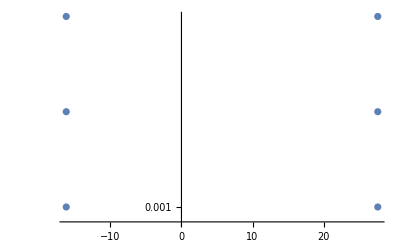

{{-27.6055,-0.001},{16.2036,-0.001},{-27.6046,-0.00125893},{16.2036,-0.00125893},{-27.6035,-0.00158489},{16.2036,-0.00158489}}

```mathematica
ListLogPlot[-taben,PlotRange->All]
taben
```

```mathematica
emin = -emin; emax = -emax;
```

```mathematica
rts1={};
Module[{pemin,pemax,pen,tabe,p},
tabe={};
dp=0.0008 emax;
p=emin;
While[p≤emax,AppendTo[tabe,p];p+=dp];
(*Print[tabe];*)
Print["Progress:"];
Print[ProgressIndicator[Dynamic[k],{1,Length[tabe]}]];
xf = 100;
Do[en=tabe[[i]];
(*Print["en = ",en];*)
k=i;
nmid=1; 
While[xt[[nmid]]<xmid,nmid++];
nmid--;

(*Print["xi = ",xi, " xf = ",xf," xmid = ", xmid];*)


AppendTo[rts1, {tabe[[i]],RootsF[tabe[[i]],50]}]

,{i,1,Length[tabe]}
]
]
```

Progress:

```mathematica
taben1={};tabphi1={};tabvec1={};
Do[AppendTo[taben1,{aHOz/ash[rts1[[n,2,1,m]]],1/Ωz rts1[[n,1]]}];AppendTo[tabphi1,{rts1[[n,2,1,m]],rts1[[n,1]]}];AppendTo[tabvec1,rts1[[n,2,2,m]]],{n,1,Length[rts1]},{m,1,Length[rts1[[n,2,1]]]}];
```

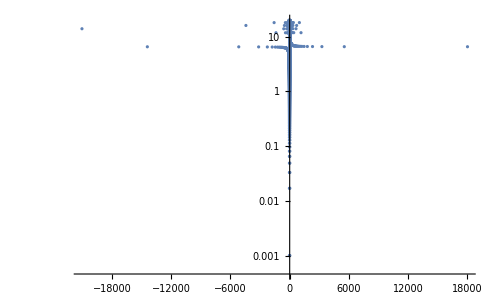

{{-27.6055,-0.001},{16.2036,-0.001},{-27.6046,-0.00125893},{16.2036,-0.00125893},{-27.6035,-0.00158489},{16.2036,-0.00158489},{-27.6021,-0.00199526},{16.2036,-0.00199526},{-27.6004,-0.00251189},{16.2036,-0.00251189},{-27.5982,-0.00316228},{16.2037,-0.00316228},{-27.5955,-0.00398107},{16.2037,-0.00398107},{-27.5921,-0.00501187},{16.2037,-0.00501187},{-27.5877,-0.00630957},{16.2038,-0.00630957},{-27.5823,-0.00794328},{16.2038,-0.00794328},{-27.5755,-0.01},{16.2039,-0.01},{-27.5668,-0.0125893},{16.204,-0.0125893},{-27.556,-0.0158489},{16.2041,-0.0158489},{-27.5424,-0.0199526},{16.2043,-0.0199526},{-27.5252,-0.0251189},{16.2045,-0.0251189},{-27.5037,-0.0316228},{16.2047,-0.0316228},{-27.4766,-0.0398107},{16.205,-0.0398107},{-27.4426,-0.0501187},{16.2054,-0.0501187},{-27.3999,-0.0630957},{16.2059,-0.0630957},{-27.3464,-0.0794328},{16.2065,-0.0794328},{-27.2793,-0.1},{16.2072,-0.1},{-27.1954,-0.125893},{16.2082,-0.125893},{-27.0906,-0.158489},{16.2094,-0.158489},{-26.9599,-0.199526},{16.2109,-0.199526},{-26.7973,-0.251189},{16.2127,-0.251189},{-26.5956,-0.316228},{16.2151,-0.316228},{-26.3465,-0.398107},{16.218,-0.398107},{-26.04,-0.501187},{16.2217,-0.501187},{-25.6652,-0.630957},{16.2263,-0.630957},{-25.2098,-0.794328},{16.2321,-0.794328},{-24.6611,-1.},{16.2392,-1.},{-24.0063,-1.25893},{16.2481,-1.25893},{-23.2339,-1.58489},{16.2591,-1.58489},{-22.3349,-1.99526},{16.2726,-1.99526},{-21.3041,-2.51189},{16.2892,-2.51189},{-20.1421,-3.16228},{16.3095,-3.16228},{-18.8557,-3.98107},{16.3342,-3.98107},{-17.4591,-5.01187},{16.3642,-5.01187},{-15.9721,-6.30957},{16.4004,-6.30957},{-14.4195,-7.94328},{16.4439,-7.94328},{-12.8281,-10.},{16.4962,-10.},{-11.2241,-12.5893},{16.5587,-12.5893},{-9.63084,-15.8489},{16.6334,-15.8489},{-8.06762,-19.9526},{16.7229,-19.9526}}

```mathematica
ListLogPlot[taben1,PlotRange->All]
taben
```

```mathematica
{1,1}
```

{1,1}

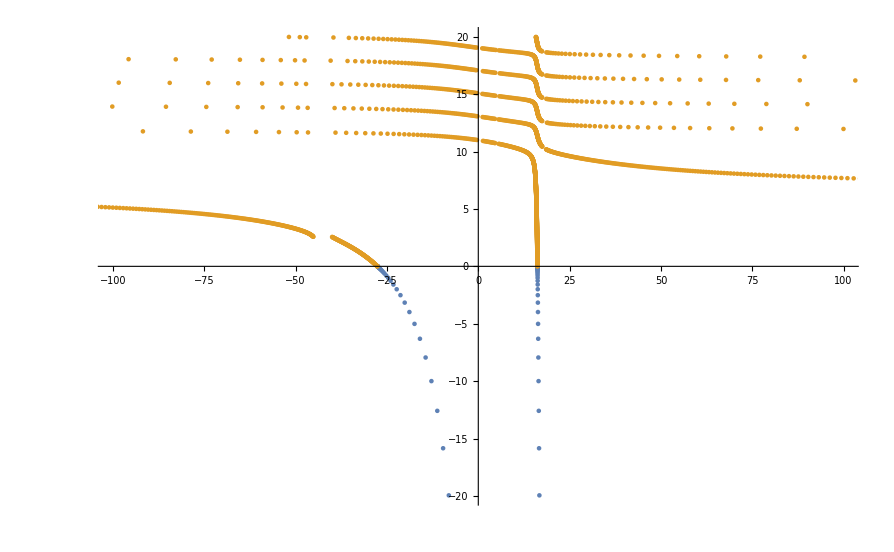

```mathematica
ListPlot[{taben,taben1},PlotRange->{{-100,100},{-20,20}}]
```

```mathematica
Export["Drop_3D_30_07.csv",Join[taben,taben1]]
```

Drop_3D_30_07.csv

```mathematica
tabb=Join[taben,taben1];
```

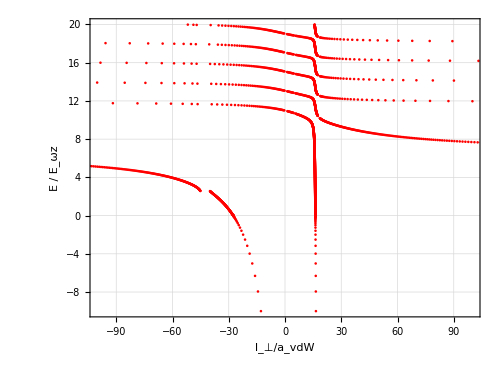

400

```mathematica
ListPlot[tabb,PlotRange->{{-100,100},{-10,20}},
AspectRatio->0.75,
Frame->True, FrameStyle->{{Directive[Thickness[0.005],Black],Directive[Thickness[0.005],Black]},{Directive[Thickness[0.005],Black],Directive[Thickness[0.005],Black]}},
PlotStyle->{Thick,{Red,Dashed}},FrameLabel->{Style["l_⊥/a_vdW",FontSize->20, FontFamily->"Times New Roman",FontWeight->Bold],Style["E / E_ωz",FontSize->20,FontWeight->Bold, FontFamily->"Times"]},GridLines->Automatic, GridLinesStyle->Directive[Thin, Dashed, LightGray],ImagePadding->50,ImageSize->500]
```

```mathematica
xf=100
energy =9;
rts=RootsF[energy,50];
tabv=rts[[2]];
tabv//MatrixForm
rts[[1,2]]
CalcPsi[rts[[1,2]],energy,tabv[[2]]];
tabpsi=Table[Table[{xt⟦n⟧,1/xt[[n]] Psi[n]⟦i⟧},{n,1,nstep}],{i,1,Lmax/2+1}];

ListLogLinearPlot[tabpsi,PlotRange->{{xi,xf},All},Joined->True,PlotLegends->Automatic]
ListPlot[tabpsi,PlotRange->{{xt[[nmid]]-0.01,xt[[nmid]]+0.03},All},Joined->True,PlotStyle->{Hue[0.],Hue[0.2],Hue[0.4],Hue[0.6],Hue[0.8]},PlotLegends->Automatic]
For[i=1,i<=Lmax/2+1,i=i+1,
Export[ToString[StringForm["Radial_functions\Psi_``.``",i,"csv"]],tabpsi[[i]],"CSV"]
]
info = {{"a",rts[[1,1]]},{"freq", N[freq]},{"aHO",N[aHO]},{"beta",N[β]},{"chanel_num",N[Lmax]}}
Export["Parameters.csv",info,"CSV"]
```

100

(0.513378 | -0.851509 | -0.0912012 | 0.0548753 | 0.00680244 | 0.000243627 | 9.45128×10^-6 | 2.90082×10^-7 | 1.79083×10^-9 | -6.69446×10^-11 | -1.41983×10^-12 | -1.36201×10^-14 | -4.13106×10^-16 | 4.27062×10^-17 | 3.28485×10^-16 | -1.25275×10^-17 | -9.25459×10^-18 | 1.21781×10^-18 | 1.58305×10^-19 | -1.92109×10^-21 | -2.55132×10^-23 | 1.48081×10^-25 | 7.9755×10^-26 | 4.18467×10^-26 | -1.41288×10^-23 | 3.10169×10^-21 | -3.47162×10^-19 | -2.17877×10^-21 | -5.52674×10^-24 | 1.4161×10^-26 | 1.71895×10^-28 | 5.59781×10^-31 | 4.68573×10^-34
-0.722195 | -0.568809 | -0.393281 | -0.0147174 | -0.0018698 | -5.68084×10^-6 | -5.8162×10^-6 | -2.79538×10^-7 | -1.45688×10^-9 | 1.10505×10^-11 | 1.10002×10^-12 | 1.12855×10^-14 | 1.97356×10^-16 | 8.35616×10^-17 | 9.50316×10^-17 | 8.97214×10^-18 | 6.99658×10^-19 | 1.45816×10^-19 | 3.78407×10^-20 | -2.07196×10^-22 | 1.56902×10^-23 | 1.27283×10^-25 | -5.38535×10^-26 | 1.31702×10^-26 | -4.37088×10^-24 | 9.59523×10^-22 | -1.07396×10^-19 | -6.77016×10^-22 | -1.86493×10^-24 | 3.22923×10^-27 | 4.99095×10^-29 | 1.73166×10^-31 | 1.75567×10^-34)

1.32789

-Graphics-

-Graphics-

{{a,0.0526269},{freq,30000.},{aHO,3.01195},{beta,4.89741},{chanel_num,64.}}

Parameters.csv

```mathematica
rts
```

{{-0.00778244,1.22053},{{0.808139,-0.570607,-0.145564,-0.0114259,-0.000455787,-0.0000111372,-1.84692×10^-7,-2.2202×10^-9,-2.0263×10^-11,-1.44842×10^-13,-7.17278×10^-16,-1.06128×10^-18,1.10977×10^-19,-6.00874×10^-22,-5.30959×10^-24,2.23135×10^-25,-2.11815×10^-28,3.7852×10^-29,-1.63872×10^-32,-1.14882×10^-35,2.51853×10^-36,7.97499×10^-37,4.96921×10^-36,-1.00056×10^-33,1.03284×10^-31,1.22462×10^-33,7.30869×10^-36,2.93543×10^-38,8.94357×10^-41,2.20716×10^-43,4.59575×10^-46,8.29582×10^-49,1.32539×10^-51},{0.865319,0.497194,0.0633152,0.00365071,0.000120076,2.55294×10^-6,3.79792×10^-8,4.17629×10^-10,3.53367×10^-12,2.3008×10^-14,3.90768×10^-17,-8.9588×10^-18,-3.36188×10^-19,-8.08828×10^-21,-8.91655×10^-23,-1.44055×10^-24,-1.02646×10^-26,-6.27284×10^-29,-3.21657×10^-31,-2.44783×10^-33,-7.90932×10^-36,2.85×10^-37,2.03077×10^-36,-4.09075×10^-34,4.22273×10^-32,4.91329×10^-34,2.86555×10^-36,1.11951×10^-38,3.30163×10^-41,7.84849×10^-44,1.56685×10^-46,2.70045×10^-49,4.11688×10^-52}}}

100

(0.634402 | -0.756631 | -0.149524 | 0.0517949 | 0.00189784 | -0.0000890088 | -5.11801×10^-6 | -2.80907×10^-8 | 1.84657×10^-9 | 6.90312×10^-11 | 1.59809×10^-12 | 2.05396×10^-14 | 2.00913×10^-16 | -6.93535×10^-17 | -2.54642×10^-16 | -1.58467×10^-16 | 2.19448×10^-17 | -9.92047×10^-19 | 9.34455×10^-20 | -1.62644×10^-21 | -1.56732×10^-23 | 7.21487×10^-25 | 6.77037×10^-27 | 3.54436×10^-28 | -3.94835×10^-31 | 3.17589×10^-33 | -6.66397×10^-35 | -2.71311×10^-35 | -2.19713×10^-37 | 3.08149×10^-39 | 5.80523×10^-37 | -1.57512×10^-34 | 2.17219×10^-32 | 2.67282×10^-34 | 1.9454×10^-36 | 7.80082×10^-39 | 1.53945×10^-42 | -2.07823×10^-43 | -1.58361×10^-45 | -7.21953×10^-48 | -2.48751×10^-50 | -7.55187×10^-53 | -2.26354×10^-55 | -6.63096×10^-58
-0.755457 | -0.435306 | 0.460553 | -0.165866 | -0.0131052 | -0.000850298 | -0.0000339285 | -5.38613×10^-7 | 4.30903×10^-9 | 4.32994×10^-10 | 7.13836×10^-12 | 7.23648×10^-14 | 1.21789×10^-16 | 1.42874×10^-16 | -5.20244×10^-17 | -7.5345×10^-16 | 6.08919×10^-17 | -5.3482×10^-18 | 4.39533×10^-19 | -1.30456×10^-20 | -1.88416×10^-22 | 1.8969×10^-24 | 4.53642×10^-26 | 8.48636×10^-28 | 4.35948×10^-29 | 1.42202×10^-31 | 1.21245×10^-33 | -6.20472×10^-34 | -5.16673×10^-36 | 2.21392×10^-38 | 3.26628×10^-36 | -8.85893×10^-34 | 1.22171×10^-31 | 1.4709×10^-33 | 1.06991×10^-35 | 4.39409×10^-38 | 1.87834×10^-41 | -1.0874×10^-42 | -8.47054×10^-45 | -3.86821×10^-47 | -1.32587×10^-49 | -4.00946×10^-52 | -1.20822×10^-54 | -3.58314×10^-57)

-0.298296

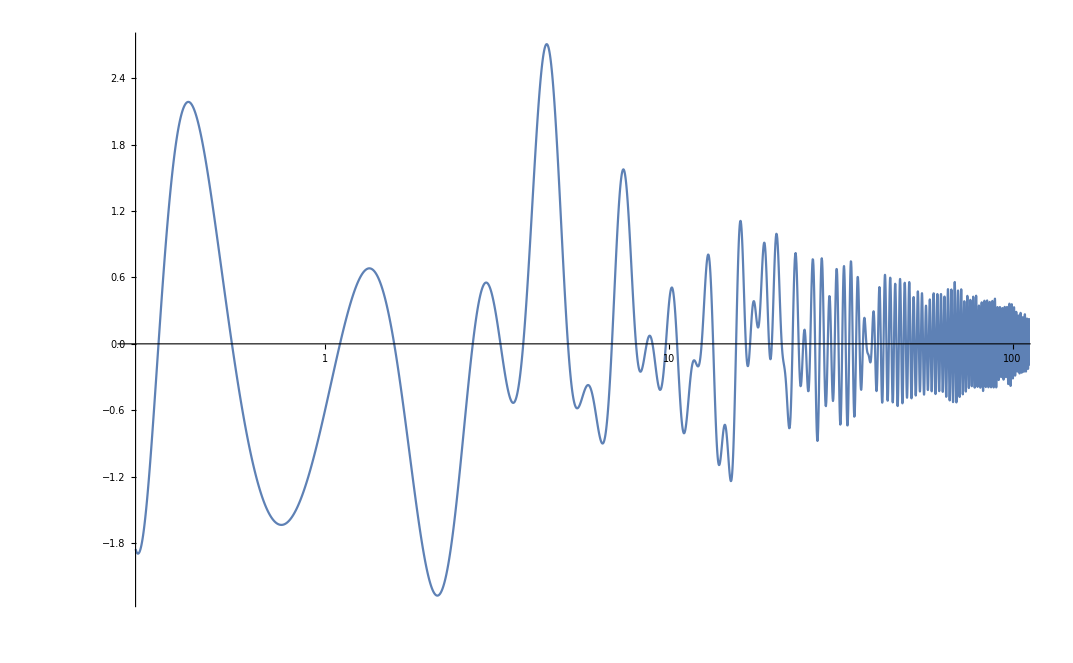

-Graphics-

{{a,-0.524141},{freq,30000.},{aHO,3.01195},{beta,4.89741},{chanel_num,32.}}

Parameters.csv

```mathematica
xf=100
energy =9;
rts=RootsF[energy,50];
tabv=rts[[2]];
tabv//MatrixForm
rts[[1,2]]
CalcPsi[rts[[1,2]],energy,tabv[[2]]];
tabpsi1=Table[{xt⟦n⟧,1/xt[[n]] Sum[Psi[n]⟦i⟧*SphericalHarmonicY[2*i,0,0,0],{i,1,Lmax/2+1}]},{n,1,nstep}];

ListLogLinearPlot[tabpsi1,PlotRange->{{xi,xf},All},Joined->True,PlotLegends->Automatic]
ListPlot[tabpsi,PlotRange->{{xt[[nmid]]-0.01,xt[[nmid]]+0.03},All},Joined->True,PlotStyle->{Hue[0.],Hue[0.2],Hue[0.4],Hue[0.6],Hue[0.8]},PlotLegends->Automatic]
For[i=1,i<=Lmax/2+1,i=i+1,
Export[ToString[StringForm["Radial_functions\Psi_``.``",i,"csv"]],tabpsi[[i]],"CSV"]
]
info = {{"a",rts[[1,1]]},{"freq", N[freq]},{"aHO",N[aHO]},{"beta",N[β]},{"chanel_num",N[Lmax]}}
Export["Parameters.csv",info,"CSV"]
```